## 100

```mathematica
WW1={{0.1,0.},{0.2,-1.0666702201226216*^-6},{0.30000000000000004,9.187078747920982*^-6},{0.4,0.00001788550426228421},{0.5,0.000053290732647651856},{0.6,0.00011765567627103429},{0.7,0.0003983514876849674},{0.7999999999999999,0.0010030874909111227},{0.8999999999999999,0.0029704772553979845},{0.9999999999999999,0.009066978072774831},{1.0999999999999999,0.023286033957274955},{1.2,0.05720781209172291},{1.3,0.11376604468976927},{1.4000000000000001,0.19215095487426498},{1.5000000000000002,0.2941487841924368},{1.6000000000000003,0.4051375737714961},{1.7000000000000004,0.5349950786172094},{1.8000000000000005,0.6594259374248531},{1.9000000000000006,0.7893438603986865},{2.0000000000000004,0.9353319212432901},{2.1000000000000005,1.051498953169258},{2.2000000000000006,1.1783386969183662},{2.3000000000000007,1.296049475497656},{2.400000000000001,1.4093842897727138},{2.500000000000001,1.524423167391128},{2.600000000000001,1.6132128212907404},{2.700000000000001,1.685649275467861},{2.800000000000001,1.7598478824173187},{2.9000000000000012,1.817857173239995},{3.0000000000000013,1.8623527848674466}};
```

```mathematica
WW2={{0.1,0.},{0.2,0.},{0.30000000000000004,0.},{0.4,0.},{0.5,0.},{0.6,0.},{0.7,0.},{0.7999999999999999,0.},{0.8999999999999999,0.},{0.9999999999999999,0.},{1.0999999999999999,0.0003957200310688715},{1.2,0.002667088485239414},{1.3,0.008493948169624534},{1.4000000000000001,0.018971346158806482},{1.5000000000000002,0.03484231373269034},{1.6000000000000003,0.0564975700551896},{1.7000000000000004,0.08536720474367843},{1.8000000000000005,0.1216689283231594},{1.9000000000000006,0.16053457107247956},{2.0000000000000004,0.21027124750976692},{2.1000000000000005,0.2626212646160044},{2.2000000000000006,0.32665272929778655},{2.3000000000000007,0.38944109855474424},{2.400000000000001,0.45584629226699647},{2.500000000000001,0.5293195746501141},{2.600000000000001,0.6022547020391618},{2.700000000000001,0.6777200712701009},{2.800000000000001,0.7589529116695976},{2.9000000000000012,0.836966945899543},{3.0000000000000013,0.9139825738301728}};
```

```mathematica
WW111=Interpolation[WW1];
WW222=Interpolation[WW2];
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

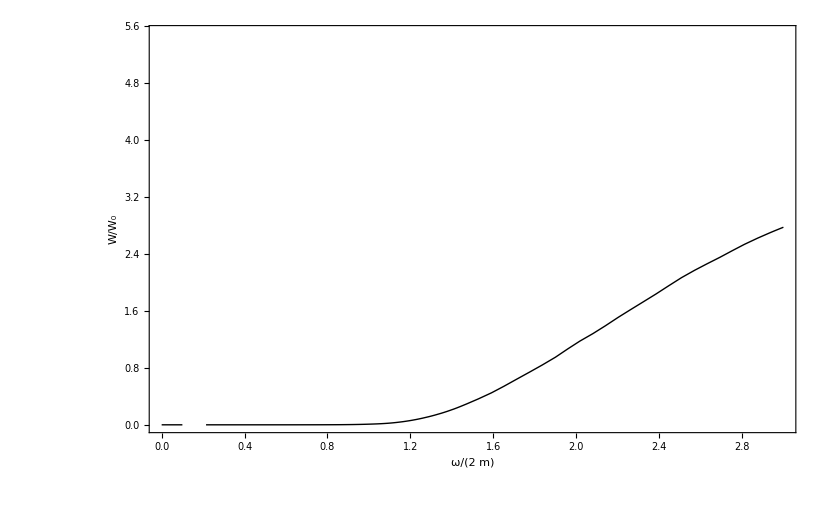

```mathematica
Plot[{WW111[x]+WW222[x],WW1120[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick,Dashed}},PlotRange->{{0,3},{0,5.5}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->{Bold,24}]
```

```mathematica
WW11={{0,0},{0.125,0},{0.25,0},{0375,0},{0.5,0},{0.625,0},{075,0},{0.875,0},{1.,0.01},{1.125,0.13280491563881811},{1.25,0.26201617804767025},{1.375,0.47579787975785043},{1.5,0.7934580203869468},{1.625,1.0446235333501386},{1.75,1.3664114003704063},{1.875,1.510588119125594},{2.,1.594376812858158},{2.125,1.533543456723447},{2.25,1.4383479552268945},{2.375,1.2462172705431058},{2.5,1.1138684862936346},{2.625,0.9958729020866698},{2.75,0.8769788249524603},{2.875,0.7787300803248336},{3.,0.6780966820784555}};
```

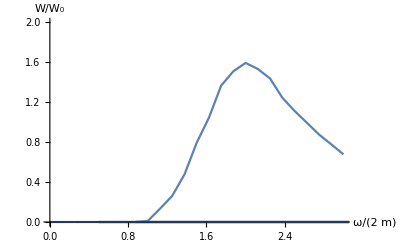

```mathematica
ListLinePlot[Re[WW11],PlotRange->{{0,3},{0,2}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

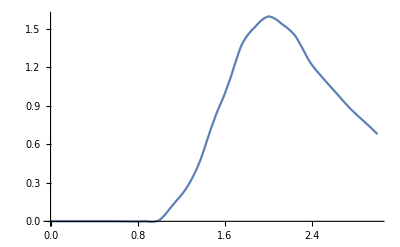

```mathematica
WWW11=Interpolation[WW11];
Plot[WWW11[x],{x,0,3}]
```

```mathematica
WW12={{1.,0.},{1.1,0},{1.2000000000000002,0},{1.3000000000000003,0.00863419837754088},{1.4000000000000004,0.01775090820870041},{1.5000000000000004,0.031246463074297934},{1.6000000000000005,0.0448688966255466},{1.7000000000000006,0.06430441695389073},{1.8000000000000007,0.08633864028729786},{1.9000000000000008,0.1135282865615031},{1.91,0.11616356101369367},{1.92,0.11943883007269632},{1.93,0.12230085072235881},{1.94,0.1252552393969102},{1.95,0.1275439206970184},{1.96,0.1309194234664932},{1.97,0.13595974879901754},{1.98,0.14018283286002337},{1.99,0.146387480427947},{2.,0.17040022163918883},{2.01,0.14635635392856536},{2.0199999999999996,0.14028527052081688},{2.0299999999999994,0.13687248802357757},{2.039999999999999,0.1346294209450728},{2.049999999999999,0.13305021781078682},{2.0599999999999987,0.13190047746780834},{2.0699999999999985,0.13104805118079466},{2.0799999999999983,0.13041468385924485},{2.089999999999998,0.1299482667519752},{2.1,0.12961458852957075},{2.2,0.12994320485160582},{2.3000000000000003,0.13281903709963647},{2.4000000000000004,0.13631063812629143},{2.5000000000000004,0.1398150045388662},{2.6000000000000005,0.14307970594613226},{2.7000000000000006,0.14596819460950192},{2.8000000000000007,0.1484181001322338},{2.900000000000001,0.15039245213482877},{3.000000000000001,0.15187592883158446}};
```

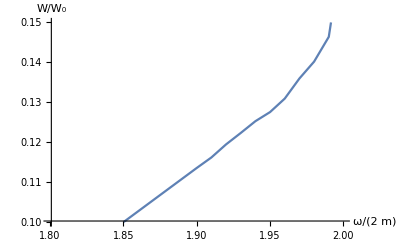

```mathematica
ListLinePlot[Re[WW12],PlotRange->{{1.8,2},{0.1,0.15}},AxesLabel->{ω/(2m),W/Subscript[W, 0]}]
```

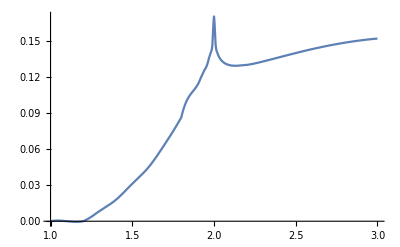

```mathematica
WWW12=Interpolation[WW12];
Plot[WWW12[x],{x,1,3}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

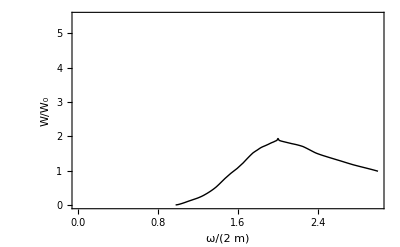

```mathematica
Plot[{WWW11[x]+2WWW12[x],WW1220[x]},{x,0,3},PlotStyle->{{Thick,Black},{Black,Thick,Dashed}},PlotRange->{{0,3},{0,5.5}},Frame->True,FrameStyle->Thick,RotateLabel->False,FrameLabel->{ω/(2m),W/Subscript[W, 0]},LabelStyle->{Bold,24}]
```